```mathematica
(*From Hansen Solubility parameters : A user's Handbook*)
(*(δd,δp,δh)in MPa need to convert in final calculation*)
asol={17.5,9.5,7.3}; (*(PLA)*)
asol={16.3,4.7,7.4}; (*(PPO)*)
(*Partial solubility parameters of poly(d,l-lactide-co-glycolide)*)
asol={17.4,8.3,10.5}; (*PLGA*)
water={15.5,16,42.3};(*(WATER)*)
(*From paper*)

water={15.5,16,42.3};(*(WATER)*)
α=0.6;
(*( mL/mol) need to convert to m^3 in final calculation*)
molvolsol=18; 
rr=8.314; (*gas constant J⋅K−1⋅mol−1)*)

a12[l1_,l2_]:=(l1[[1]]-l2[[1]])^2+0.25(l1[[2]]-l2[[2]])^2+0.25(l1[[3]]-l2[[3]])^2;
chisol[l1_,l2_,vol_,tt_]:=(α vol a12[l1,l2])/(rr tt);
"χ_pla,water";
nn=1; (*(used in paper n=232 n=928)*)
chisol[asol,water,molvolsol,273.15+25]*(10^-6)*(10^6)*nn
```

1.18178

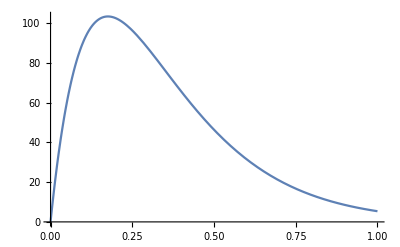

{0.75,0.625,0.520833,0.434028,0.36169,0.301408,0.251173,0.209311,0.174426,0.145355,0.121129,0.100941,0.0841175,0.0700979,0.0584149}

```mathematica
(*Calculation of chemical potential for explicit solvent*)
fa=0.5;
fb=1-fa;
tt[phibar_]=(2*fa*fb*chiAB*phibar+(1-phibar) *(chias fa+chibs fb));
μ[phibar_]=Log[phibar ]+tt[phibar];
Plot[phibar Exp[tt[phibar]],{phibar,0,1},PlotRange->All]
```

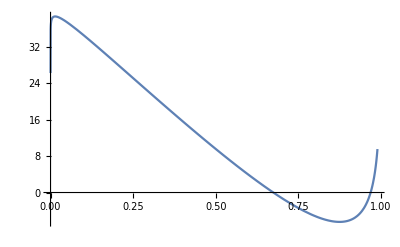

{6.73241×10^16,{phibar→0.0140524}}

{0.00209092,{phibar→0.842319}}

{0.3,0.25,0.208333,0.173611,0.144676,0.120563,0.100469,0.0837245,0.0697704,0.058142}

{21.9856,25.1786,27.8433,30.0548,31.8809,33.381,34.6065,35.6012,36.4023,37.0412}

{1.06008×10^9,2.15207×10^10,2.57599×10^11,1.9598×10^12,1.01413×10^13,3.78806×10^13,1.07513×10^14,2.4225×10^14,4.49762×10^14,7.10018×10^14}

17.9927

```mathematica
(*Calculation of chemical potential for implicit solvent*)
Clear[phibar,μ,tt]
fa=0.5;
fb=1-fa;
vs=0.1;
zeta=1.0/vs;
chieffAA=-2 chias;
chieffAB=chiAB-chias-chibs;
chieffBB=-2 chibs;
tt[phibar_]=-zeta*Log[(1.0-phibar)]+phibar*(chieffAA fa fa+2.0*chieffAB fa fb+chieffBB fb fb)+ chias fa+chibs fb;
μ[phibar_]=Log[phibar]+tt[phibar];
Plot[ Exp[μ[phibar]],{phibar,0,0.9},PlotRange->All];
Plot[ μ[phibar],{phibar,0,0.99},PlotRange->All]

FindMaximum[Exp[μ[phibar]],{phibar,0.1}]
FindMinimum[{Exp[μ[phibar]],0.1<phibar<1},{phibar,0.1}]
beg=0.3;
n=10;
phibars=Table[beg/1.2^i,{i,0,n-1}]
mus=μ[phibars]
mult=phibars Exp[μ[phibars]]
μ[0.000000000005]
```

```mathematica
InverseFourierTransform[(-ω^2 s),ω,t]
```

```mathematica
Assuming[s<0,Integrate[Exp[ⅈ k r]Exp[k^2 s],{k,-Infinity,Infinity}]]
```

(ⅇ^(r^2/(4 s)) √π)/(√-s)

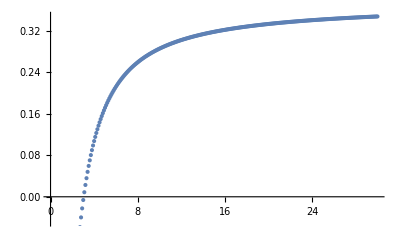

```mathematica
fo=0.2;
go=Table[i*0.1,{i,1,300}];
fa=0.5;
co=Table[FindRoot[fo+(1-fo)x+(1-x)/go[[i]](1-Exp[-go[[i]](1-fo)])==fa,{x,2000}][[1]][[2]],{i,1,Length[go]}];
data=Transpose@{go,co};
ListPlot[data]
(*go=Table[FindRoot[fo[[i]]==fa,{x,0.5}]
{x->0.860334}*)
```

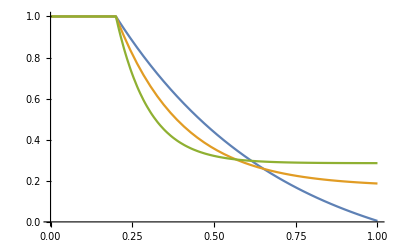

{0.5,0.5}

```mathematica
g[s_,i_]:=UnitStep[fo-s]+UnitStep[s-fo]((1-co[[i]])Exp[-go[[i]](s-fo)]+co[[i]])
Plot[{g[s,20],g[s,50],g[s,100]},{s,0,1}]
NIntegrate[{g[s,20],g[s,100]},{s,0,1}]
```